```mathematica
(* In this script, the neutrino fluxes are calculated and plotted for the three initial conditions considered in the mnaucript. 
Notation wise, NH=Normal Hierarchy, IH=Inverted Hierarchy,EU=Early Universe and LU=Late Universe. We start by listing the parameters needed, which are retrieved from the ``Review of Particle Physics'', reference [32] of the manuscript.*)
```

```mathematica
Co[x_]:=Cos[x];
S[x_]:=Sin[x];
(*This is Subscript[θ, 12]*)
a=ArcSin[Sqrt[0.307]];
(*This is Subscript[θ, 13]*)
b=ArcSin[Sqrt[0.0218]];
(*This is Subscript[θ, 23] in the NH*)
NHc=ArcSin[Sqrt[0.545]];
(*This is Subscript[θ, 23] in the IH*)
IHc=ArcSin[Sqrt[0.547]];
(*CP violating phase δ*)
d=1.04*Pi;
(*Subscript[Δm, 21]^2=Subscript[m, 2]^2-Subscript[m, 1]^2*)
Dm21=7.53*10^-5;
(*Subscript[Δm, 32]^2=Subscript[m, 3]^2-Subscript[m, 2]^2 in the IH*)
Dm32IH=-2.546*10^-3;
(*Subscript[Δm, 32]^2=Subscript[m, 3]^2-Subscript[m, 2]^2 in the NH*)
Dm32NH=2.453*10^-3;
(*Subscript[Δm, 31]^2=Subscript[m, 3]^2-Subscript[m, 1]^2 in the NH*)
Dm31NH=Dm32NH+Dm21;
(*Subscript[Δm, 31]^2=Subscript[m, 3]^2-Subscript[m, 1]^2 in the IH*)
Dm31IH=Dm32IH+Dm21;
(*This is a typical neutrino energy detected at neutrino observatories. As long as the value is high enough to be in the ultra-high energy regime, the excat value does not affect the results*)
E0=10^16.;
(*In natural units, Subscript[H, 0]=2.13 x10^-33 xh. We keep this infinitesimal prefactor seperate to better study the effect of choosing different h. In reality 
this prefactor can be cast away by a renormalization of the scale factor and redshift*)
H0=2.13*10^-33.;
fac=1/(H0*E0);
(*Matter density parameter as measured by the Planck mission (reference [3] in the mansucript)Subscript[Ω, m0]*)
Om0=0.315;
(*Dark Energy(DE) density parameter as measured by the Planck mission (reference [3] in the mansucript)Subscript[Ω, Λ0]*)
Ol0=0.685;
(*Hubble parameter at EU, i.e. h^EU*)
EUh=0.675;
(*Hubble parameter at LU, i.e. h^LU*)
LUh=0.732;
(*This is the integrand in eq.(11) of the mansucript*)
Subscript[F, Λ][z_]:= (Om0*(1+z)^7.+Ol0*(1+z)^4.)^-.5;
int=Assuming[z>=0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]];
(*This is Δλ of the mnasucript, eq.(11), for EU*)
EUomAn=int/EUh;
(*This is Δλ of the mnasucript, eq.(11), for LU*)
LUomAn=int/LUh;
(*This is the PMNS matrix, eq.(6) of the mnasucript, for NH*)
NHU={{Co[a]*Co[b],S[a]*Co[b],S[b]*(Co[d]-I*S[d])},{-S[a]*Co[NHc]-S[b]*S[NHc]*Co[a]*(Co[d]+I*S[d]),Co[a]*Co[NHc]-S[a]*S[NHc]*S[b]*(Co[d]+I*S[d]),S[NHc]*Co[b]},{S[a]*S[NHc]-S[b]*Co[a]*Co[NHc]*(Co[d]+I*S[d]),-S[NHc]*Co[a]-S[a]*S[b]*Co[NHc]*(Co[d]+I*S[d]),Co[b]*Co[NHc]}};
(*This is the PMNS matrix, eq.(6) of the mnasucript, for NH*)
IHU={{Co[a]*Co[b],S[a]*Co[b],S[b]*(Co[d]-I*S[d])},{-S[a]*Co[IHc]-S[b]*S[IHc]*Co[a]*(Co[d]+I*S[d]),Co[a]*Co[IHc]-S[a]*S[IHc]*S[b]*(Co[d]+I*S[d]),S[IHc]*Co[b]},{S[a]*S[IHc]-S[b]*Co[a]*Co[IHc]*(Co[d]+I*S[d]),-S[IHc]*Co[a]-S[a]*S[b]*Co[IHc]*(Co[d]+I*S[d]),Co[b]*Co[IHc]}};
```

```mathematica
(*U^† for NH*)
NHUdag=ConjugateTranspose[NHU];
MatrixForm[NHUdag]
(*U^† for IH*)
IHUdag=ConjugateTranspose[IHU];
```

(0.823342 | -0.283721-0.0113726 ⅈ | 0.491297-0.0103912 ⅈ
0.548003 | 0.621447-0.00756941 ⅈ | -0.559813-0.00691623 ⅈ
-0.146484-0.0185052 ⅈ | 0.73015 | 0.667144)

```mathematica
(*The fllowing two lines are to check the Unitarity condition of the PMNS matrix, to make sure there was no error in writing them, for both NH and IH*)
```

```mathematica
MatrixForm[FullSimplify[NHUdag . NHU]];
MatrixForm[FullSimplify[IHUdag . IHU]];
```

```mathematica
(*The set of initial transition amplitudes conditions, Ψ^ini considered in the mansucript, ND, MD and PD, compactified in one matrix*)
TPsi0={{1,0,0},{0,1,0},{1/Sqrt[5],2/Sqrt[5],0}};
MatrixForm[TPsi0]
```

(1 | 0 | 0
0 | 1 | 0
1/(√5) | 2/(√5) | 0)

```mathematica
(*Initial transition amplitudes conditions in the mass basis, Φ of the manuscript, in the NH. Basically eq.(8) of the manuscript*)
TNHPhi0={NHUdag . TPsi0[[1]],NHUdag . TPsi0[[2]],NHUdag . TPsi0[[3]]};
MatrixForm[TNHPhi0]
(*Initial transition amplitudes conditions in the mass basis, Φ of the manuscript, in the IH. Basically eq.(8) of the manuscript*)
TIHPhi0={IHUdag . TPsi0[[1]],IHUdag . TPsi0[[2]],IHUdag . TPsi0[[3]]};
MatrixForm[TIHPhi0]
```

(0.823342+0. ⅈ | 0.548003+0. ⅈ | -0.146484-0.0185052 ⅈ
-0.283721-0.0113726 ⅈ | 0.621447-0.00756941 ⅈ | 0.73015+0. ⅈ
0.114442-0.010172 ⅈ | 0.800914-0.00677028 ⅈ | 0.587556-0.00827579 ⅈ)

(0.823342+0. ⅈ | 0.548003+0. ⅈ | -0.146484-0.0185052 ⅈ
-0.282734-0.0113934 ⅈ | 0.620322-0.00758328 ⅈ | 0.731488+0. ⅈ
0.115325-0.0101906 ⅈ | 0.799907-0.0067827 ⅈ | 0.588754-0.00827579 ⅈ)

```mathematica
(*The evolving factors for the mass basis transition amplitudes, as written in eq.(10) of the mnasucript*)
```

```mathematica
T=DiagonalMatrix[{Co[m1^2*Intz/2]-I*S[m1^2*Intz/2],Co[m2^2*Intz/2]-I*S[m2^2*Intz/2],Co[m3^2*Intz/2]-I*S[m3^2*Intz/2]}];
(*The evolved transition amplitude, in the mass basis, with redshift, as given in eq.(10) of the mansucript, for NH*)
TNHPhi=FullSimplify[{T.TNHPhi0[[1]],T.TNHPhi0[[2]],T.TNHPhi0[[3]]}];
MatrixForm[TNHPhi]
(*The evolved transition amplitude, in the mass basis, with redshift, as given in eq.(10) of the mansucript, for IH*)
TIHPhi=FullSimplify[{T.TIHPhi0[[1]],T.TIHPhi0[[2]],T.TIHPhi0[[3]]}];
MatrixForm[TIHPhi]
```

(0.823342 ⅇ^(-1/2 ⅈ Intz m1^2) | 0.548003 ⅇ^(-1/2 ⅈ Intz m2^2) | (-0.146484-0.0185052 ⅈ) ⅇ^(-1/2 ⅈ Intz m3^2)
(-0.283721-0.0113726 ⅈ) ⅇ^(-1/2 ⅈ Intz m1^2) | (0.621447-0.00756941 ⅈ) ⅇ^(-1/2 ⅈ Intz m2^2) | 0.73015 ⅇ^(-1/2 ⅈ Intz m3^2)
(0.114442-0.010172 ⅈ) ⅇ^(-1/2 ⅈ Intz m1^2) | (0.800914-0.00677028 ⅈ) ⅇ^(-1/2 ⅈ Intz m2^2) | (0.587556-0.00827579 ⅈ) ⅇ^(-1/2 ⅈ Intz m3^2))

(0.823342 ⅇ^(-1/2 ⅈ Intz m1^2) | 0.548003 ⅇ^(-1/2 ⅈ Intz m2^2) | (-0.146484-0.0185052 ⅈ) ⅇ^(-1/2 ⅈ Intz m3^2)
(-0.282734-0.0113934 ⅈ) ⅇ^(-1/2 ⅈ Intz m1^2) | (0.620322-0.00758328 ⅈ) ⅇ^(-1/2 ⅈ Intz m2^2) | 0.731488 ⅇ^(-1/2 ⅈ Intz m3^2)
(0.115325-0.0101906 ⅈ) ⅇ^(-1/2 ⅈ Intz m1^2) | (0.799907-0.0067827 ⅈ) ⅇ^(-1/2 ⅈ Intz m2^2) | (0.588754-0.00827579 ⅈ) ⅇ^(-1/2 ⅈ Intz m3^2))

```mathematica
(*The evolved transition amplitude, in the flavor basis, with redshift, as given in eq.(10) of the mansucript, for NH*)
TNHPsi={NHU . TNHPhi[[1]],NHU . TNHPhi[[2]],NHU . TNHPhi[[3]]};
MatrixForm[TNHPsi];
(*The evolved transition amplitude, in the flavor basis, with redshift, as given in eq.(10) of the mansucript, for IH*)
TIHPsi={IHU . TIHPhi[[1]],IHU . TIHPhi[[2]],IHU . TIHPhi[[3]]};
MatrixForm[TNHPsi];
(*Here we present analytical expression for the total flux from all initial conditions for each neutrino flavor, in both hierarchies*)
(*On the techinical side, the flux of a certain flavor, as argued in the manuscript, is simply the sum of transition probabilities to that flavor, which is the modulus squared of transition amplitudes. This is what we are calculating below*)
Print["NHFlux-e="]
(*Subscript[ν, e] flux for NH*)
NHFluxe=FullSimplify[TrigReduce[ComplexExpand[Re[TNHPsi[[All,1]]]^2+Im[TNHPsi[[All,1]]]^2]]];
MatrixForm[NHFluxe]
Print["IHFluxe="]
(*Subscript[ν, e] flux for IH*)
IHFluxe=FullSimplify[TrigReduce[ComplexExpand[Re[TIHPsi[[All,1]]]^2+Im[TIHPsi[[All,1]]]^2]]];
MatrixForm[IHFluxe]
Print["NHFluxmu="]
(*Subscript[ν, μ] flux for NH*)
NHFluxmu=FullSimplify[TrigReduce[ComplexExpand[Re[TNHPsi[[All,2]]]^2+Im[TNHPsi[[All,2]]]^2]]];
MatrixForm[NHFluxmu]
Print["IHFluxmu="]
(*Subscript[ν, μ] flux for IH*)
IHFluxmu=FullSimplify[TrigReduce[ComplexExpand[Re[TIHPsi[[All,2]]]^2+Im[TIHPsi[[All,2]]]^2]]];
MatrixForm[IHFluxmu]
Print["NHFluxtau="]
(*Subscript[ν, τ] flux for NH*)
NHFluxtau=FullSimplify[TrigReduce[ComplexExpand[Re[TNHPsi[[All,3]]]^2+Im[TNHPsi[[All,3]]]^2]]];
MatrixForm[NHFluxtau]
Print["IHFluxtau="]
(*Subscript[ν, τ] flux for IH*)
IHFluxtau=FullSimplify[TrigReduce[ComplexExpand[Re[TIHPsi[[All,3]]]^2+Im[TIHPsi[[All,3]]]^2]]];
MatrixForm[IHFluxtau]
```

NHFlux-e=

(0.550198+0.407152 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0295561 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.0130934 Cos[1/2 Intz (m2-m3) (m2+m3)]
0.182273-0.159029 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0497164 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.0729604 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.00831557 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.00831557 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.00831557 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.209126+0.0827733 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.016393 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.0755059 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.00665245 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.000838373 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.0099709 Sin[1/2 Intz (m2-m3) (m2+m3)])

IHFluxe=

(0.550198+0.407152 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0295561 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.0130934 Cos[1/2 Intz (m2-m3) (m2+m3)]
0.181518-0.158188 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0496329 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.0729622 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.00831248 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.00831248 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.00831248 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.20881+0.083307 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.016552 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.0755652 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.00664999 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.000854574 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.00997452 Sin[1/2 Intz (m2-m3) (m2+m3)])

NHFluxmu=

(0.182273-0.159029 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0497164 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.0729604 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.00831557 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.00831557 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.00831557 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.439909+0.0622851 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0859677 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.411839 Cos[1/2 Intz (m2-m3) (m2+m3)]
0.432931-0.0321945 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0278105 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.427074 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.00428892 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.00320191 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.00760737 Sin[1/2 Intz (m2-m3) (m2+m3)])

IHFluxmu=

(0.181518-0.158188 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0496329 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.0729622 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.00831248 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.00831248 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.00831248 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.440831+0.0616296 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0856851 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.411854 Cos[1/2 Intz (m2-m3) (m2+m3)]
0.432852-0.032231 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0280357 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.427415 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.00428448 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.00322008 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.00760901 Sin[1/2 Intz (m2-m3) (m2+m3)])

NHFluxtau=

(0.267528-0.248123 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0792725 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.059867 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.00831557 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.00831557 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.00831557 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.377818+0.0967444 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.135684 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.338878 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.00831557 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.00831557 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.00831557 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.357944-0.0505788 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0442035 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.351568 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.00236354 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.00236354 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.00236354 Sin[1/2 Intz (m2-m3) (m2+m3)])

IHFluxtau=

(0.268284-0.248964 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.079189 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.0598688 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.00831248 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.00831248 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.00831248 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.377651+0.0965587 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.135318 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.338892 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.00831248 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.00831248 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.00831248 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.358338-0.0510761 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0445876 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.35185 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.0023655 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.0023655 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.0023655 Sin[1/2 Intz (m2-m3) (m2+m3)])

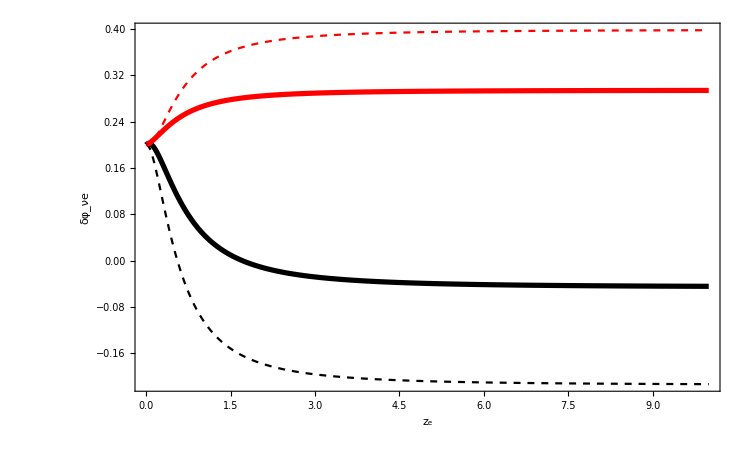

```mathematica
(*After having calculated the general analytical expressions, we now specify to the two cases of EU and LU and plot each of their evolution with redshift*)
Max21EU=MaxValue[{Dm21*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/EUh,0<z<10},z];
Max21LU=MaxValue[{Dm21*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/LUh,0<z<10},z];
Max31NHEU=MaxValue[{Dm31NH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/EUh,0<z<10},z];
Max31NHLU=MaxValue[{Dm31NH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/LUh,0<z<10},z];
Max31IHEU=MaxValue[{Abs[Dm31IH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/EUh],0<z<10},z];
Max31IHLU=MaxValue[{Abs[Dm31IH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/LUh],0<z<10},z];
Max32NHEU=MaxValue[{Dm32NH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/EUh,0<z<10},z];
Max32NHLU=MaxValue[{Dm32NH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/LUh,0<z<10},z];
Max32IHEU=MaxValue[{Abs[Dm32IH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/EUh],0<z<10},z];
Max32IHLU=MaxValue[{Abs[Dm32IH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/LUh],0<z<10},z];
(*Subscript[ν, e] flux for NH-EU*)

NHTotFluxeEU[z_]=Total[NHFluxe]/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*EUomAn*fac/(Max21EU)*N[Drop@@RealDigits[Round[N[Max21EU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31NH*EUomAn*fac/(Max31NHEU)*N[Drop@@RealDigits[Round[N[Max31NHEU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32NH*EUomAn*fac/(Max32NHEU)*N[Drop@@RealDigits[Round[N[Max32NHEU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi)};
(*Subscript[ν, e] flux for NH-LU*)
NHTotFluxeLU[z_]=Total[NHFluxe]/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*LUomAn*fac/(Max21LU)*N[Drop@@RealDigits[Round[N[Max21LU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31NH*LUomAn*fac/(Max31NHLU)*N[Drop@@RealDigits[Round[N[Max31NHLU/(2*Pi)],1*^-7]]*10^-5//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32NH*LUomAn*fac/(Max32NHLU)*N[Drop@@RealDigits[Round[N[Max32NHLU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi)};
(*Subscript[ν, e] flux for IH-EU*)
IHTotFluxeEU[z_]=Total[IHFluxe]/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*EUomAn*fac/(Max21EU)*N[Drop@@RealDigits[Round[N[Max21EU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31IH*EUomAn*fac/(Max31IHEU)*N[Drop@@RealDigits[Round[N[Max31IHEU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32IH*EUomAn*fac/(Max32IHEU)*N[Drop@@RealDigits[Round[N[Max32IHEU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi)};
(*Subscript[ν, e] flux for IH-LU*)
IHTotFluxeLU[z_]=Total[IHFluxe]/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*LUomAn*fac/(Max21LU)*N[Drop@@RealDigits[Round[N[Max21LU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31IH*LUomAn*fac/(Max31IHLU)*N[Drop@@RealDigits[Round[N[Max31IHLU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32IH*LUomAn*fac/(Max32IHLU)*N[Drop@@RealDigits[Round[N[Max32IHLU/(2*Pi)],1*^-6]]*10^-6//FromDigits]*2*Pi)};
(*Here we plot the fractional difference between emmitted and observed fluxes, as explained in eq.(15) of the manuscript*)
Plot[{NHTotFluxeEU[z]-1,NHTotFluxeLU[z]-1,IHTotFluxeEU[z]-1,IHTotFluxeLU[z]-1},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Directive[Thickness[0.005]]},{Black,Dashed},{Red,Dashed}},FrameLabel->{Style["z_e",24,Bold],Style["δφ_νe",24,Bold]},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],24,FontFamily->"Helvetica",Bold]]
(*Export["Path",%,name.pdf,"PDF"]*)
```

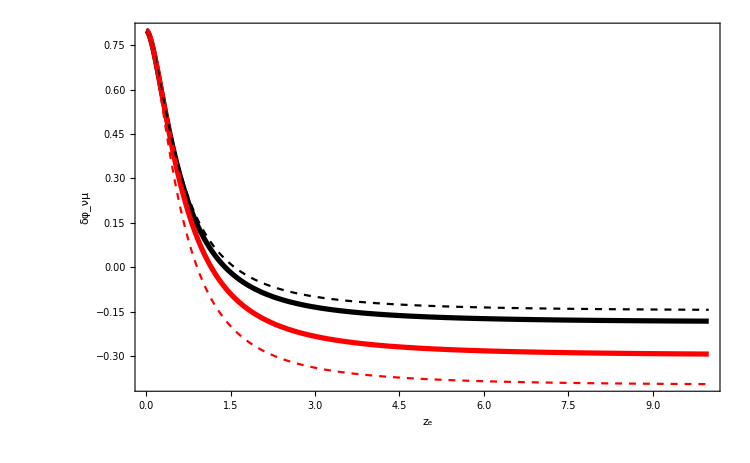

```mathematica
(*Subscript[ν, μ] flux for NH-EU*)
NHTotFluxmuEU[z_]=Total[NHFluxmu]/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*EUomAn*fac/(Max21EU)*N[Drop@@RealDigits[Round[N[Max21EU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31NH*EUomAn*fac/(Max31NHEU)*N[Drop@@RealDigits[Round[N[Max31NHEU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32NH*EUomAn*fac/(Max32NHEU)*N[Drop@@RealDigits[Round[N[Max32NHEU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi)};
(*Subscript[ν, μ] flux for NH-LU*)
NHTotFluxmuLU[z_]=Total[NHFluxmu]/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*LUomAn*fac/(Max21LU)*N[Drop@@RealDigits[Round[N[Max21LU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31NH*LUomAn*fac/(Max31NHLU)*N[Drop@@RealDigits[Round[N[Max31NHLU/(2*Pi)],1*^-7]]*10^-5//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32NH*LUomAn*fac/(Max32NHLU)*N[Drop@@RealDigits[Round[N[Max32NHLU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi)};
(*Subscript[ν, μ] flux for IH-EU*)
IHTotFluxmuEU[z_]=Total[IHFluxmu]/.
{(m1-m2)*(m1+m2)*Intz->(-Dm21*EUomAn*fac/(Max21EU)*N[Drop@@RealDigits[Round[N[Max21EU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31IH*EUomAn*fac/(Max31IHEU)*N[Drop@@RealDigits[Round[N[Max31IHEU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32IH*EUomAn*fac/(Max32IHEU)*N[Drop@@RealDigits[Round[N[Max32IHEU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi)};
(*Subscript[ν, μ] flux for IH-LU*)
IHTotFluxmuLU[z_]=Total[IHFluxmu]/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*LUomAn*fac/(Max21LU)*N[Drop@@RealDigits[Round[N[Max21LU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31IH*LUomAn*fac/(Max31IHLU)*N[Drop@@RealDigits[Round[N[Max31IHLU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32IH*LUomAn*fac/(Max32IHLU)*N[Drop@@RealDigits[Round[N[Max32IHLU/(2*Pi)],1*^-6]]*10^-6//FromDigits]*2*Pi)};
Plot[{NHTotFluxmuEU[z]-1,NHTotFluxmuLU[z]-1,IHTotFluxmuEU[z]-1,IHTotFluxmuLU[z]-1},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Directive[Thickness[0.005]]},{Black,Dashed},{Red,Dashed}},FrameLabel->{Style["z_e",24,Bold],Style["δφ_νμ",24,Bold]},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],24,FontFamily->"Helvetica",Bold]]
(*Export["Path",%,name.pdf,"PDF"]*)
```

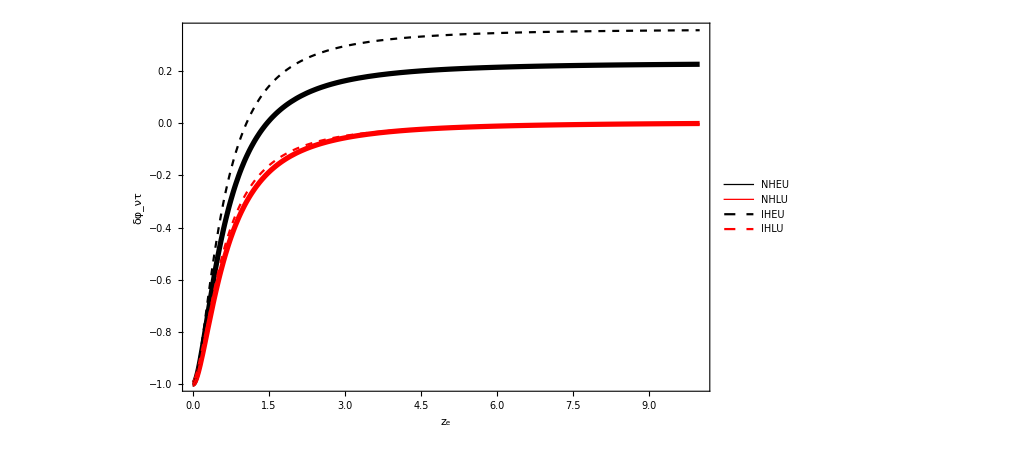

```mathematica
(*Subscript[ν, τ] flux for NH-EU*)
NHTotFluxtauEU[z_]=Total[NHFluxtau]/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*EUomAn*fac/(Max21EU)*N[Drop@@RealDigits[Round[N[Max21EU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31NH*EUomAn*fac/(Max31NHEU)*N[Drop@@RealDigits[Round[N[Max31NHEU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32NH*EUomAn*fac/(Max32NHEU)*N[Drop@@RealDigits[Round[N[Max32NHEU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi)};
(*Subscript[ν, τ] flux for NH-LU*)
NHTotFluxtauLU[z_]=Total[NHFluxtau]/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*LUomAn*fac/(Max21LU)*N[Drop@@RealDigits[Round[N[Max21LU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31NH*LUomAn*fac/(Max31NHLU)*N[Drop@@RealDigits[Round[N[Max31NHLU/(2*Pi)],1*^-7]]*10^-5//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32NH*LUomAn*fac/(Max32NHLU)*N[Drop@@RealDigits[Round[N[Max32NHLU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi)};
(*Subscript[ν, τ] flux for IH-EU*)
IHTotFluxtauEU[z_]=Total[IHFluxtau]/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*EUomAn*fac/(Max21EU)*N[Drop@@RealDigits[Round[N[Max21EU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31IH*EUomAn*fac/(Max31IHEU)*N[Drop@@RealDigits[Round[N[Max31IHEU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32IH*EUomAn*fac/(Max32IHEU)*N[Drop@@RealDigits[Round[N[Max32IHEU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi)};
(*Subscript[ν, τ] flux for IH-LU*)
IHTotFluxtauLU[z_]=Total[IHFluxtau]/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*LUomAn*fac/(Max21LU)*N[Drop@@RealDigits[Round[N[Max21LU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31IH*LUomAn*fac/(Max31IHLU)*N[Drop@@RealDigits[Round[N[Max31IHLU/(2*Pi)],1*^-4]]*10^-4//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32IH*LUomAn*fac/(Max32IHLU)*N[Drop@@RealDigits[Round[N[Max32IHLU/(2*Pi)],1*^-6]]*10^-6//FromDigits]*2*Pi)};
Plot[{NHTotFluxtauEU[z]-1,NHTotFluxtauLU[z]-1,IHTotFluxtauEU[z]-1,IHTotFluxtauLU[z]-1},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Directive[Thickness[0.005]]},{Black,Dashed},{Red,Dashed}},PlotLegends->Placed[{Style["NHEU",24],Style["NHLU",24],Style["IHEU",24],Style["IHLU",24]},{Right,Bottom}],FrameLabel->{Style["z_e",24,Bold],Style["δφ_ντ",24,Bold]},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],22,FontFamily->"Helvetica",Bold]]
(*Export["Path",%,name.pdf,"PDF"]*)
```

```mathematica
(*Here we plot the fractional differnce between EU and LU for each flux, as given in eq.(16) of the mansucript*)
```

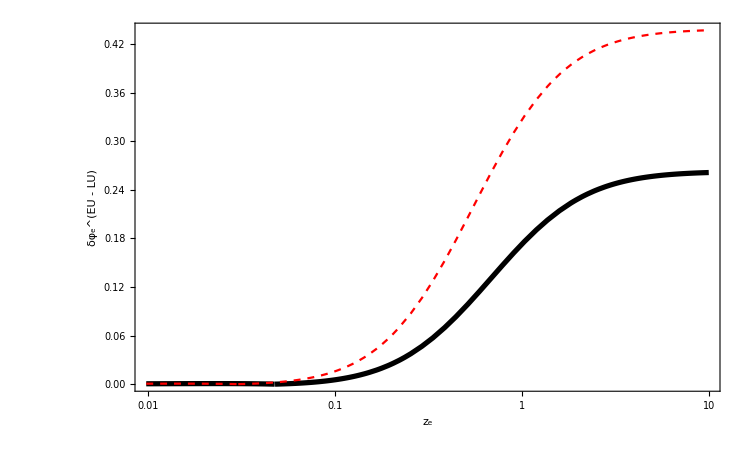

```mathematica
LogLinearPlot[{Abs[(NHTotFluxeEU[z]-NHTotFluxeLU[z])/Max[NHTotFluxeEU[z],NHTotFluxeLU[z]]],Abs[(IHTotFluxeEU[z]-IHTotFluxeLU[z])/Max[IHTotFluxeEU[z],IHTotFluxeLU[z]]]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Dashed}},FrameLabel->{Style["z_e",24,Bold],Style["δφ_e^(EU - LU)",24,Bold]},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],24,FontFamily->"Helvetica",Bold]]
(*Export["Path",%,name.pdf,"PDF"]*)
```

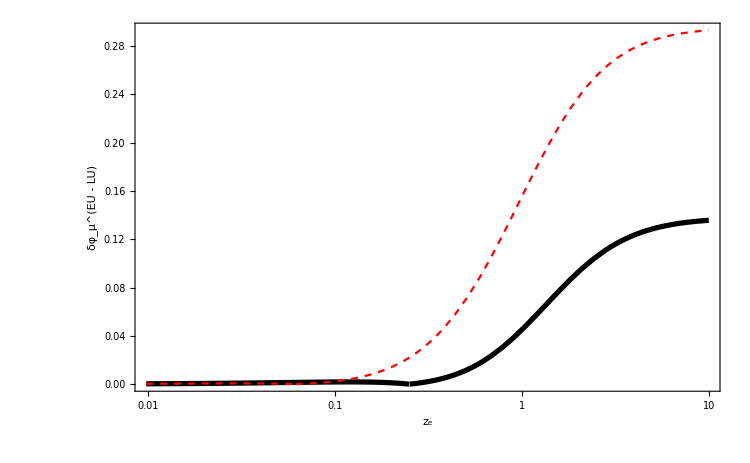

```mathematica
LogLinearPlot[{Abs[(NHTotFluxmuEU[z]-NHTotFluxmuLU[z])/Max[NHTotFluxmuEU[z],NHTotFluxmuLU[z]]],Abs[(IHTotFluxmuEU[z]-IHTotFluxmuLU[z])/Max[IHTotFluxmuEU[z],IHTotFluxmuLU[z]]]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Dashed}},FrameLabel->{Style["z_e",24,Bold],Style["δφ_μ^(EU - LU)",24,Bold]},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],24,FontFamily->"Helvetica",Bold]]
(*Export["Path",%,name.pdf,"PDF"]*)
```

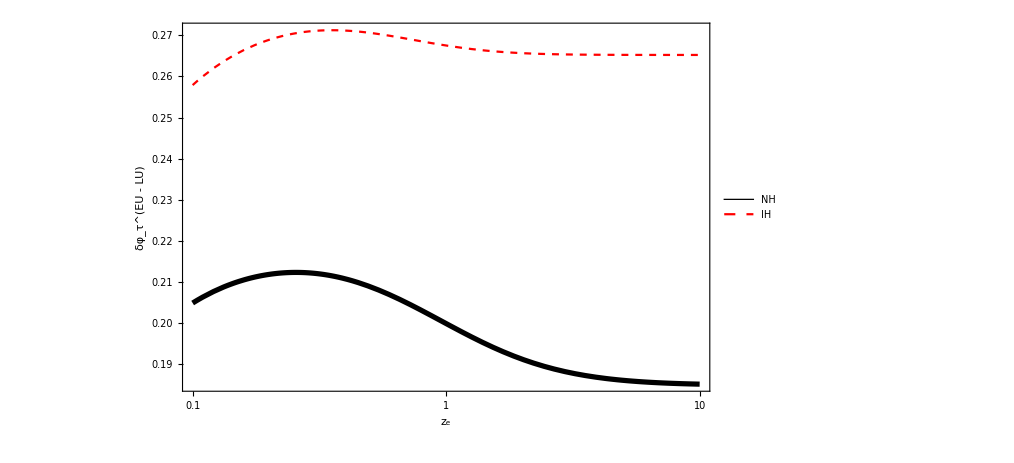

```mathematica
LogLinearPlot[{Abs[(NHTotFluxtauEU[z]-NHTotFluxtauLU[z])/Max[NHTotFluxtauEU[z],NHTotFluxtauLU[z]]],Abs[(IHTotFluxtauEU[z]-IHTotFluxtauLU[z])/Max[IHTotFluxtauEU[z],IHTotFluxtauLU[z]]]},{z,0.1,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Dashed}},PlotLegends->Placed[{Style["NH",24],Style["IH",24]},{Right,Center}],FrameLabel->{Style["z_e",24,Bold],Style["δφ_τ^(EU - LU)",24,Bold]},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],24,FontFamily->"Helvetica",Bold]]
(*Export["Path",%,name.pdf,"PDF"]*)
```